-Graphics3D-

-Graphics3D-

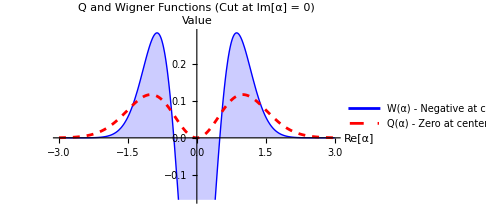

```mathematica
(*Definition of quasi-probability functions Q and W for single-photon state|1⟩*)(*1. Q function (Husimi) for|1⟩ state*)(*Q(α)=1/π|α|^2 Exp[-|α|^2]*)QFunctionSinglePhoton[x_,y_]:=(1/Pi)*(x^2+y^2)*Exp[-(x^2+y^2)]

(*2. Wigner function for|1⟩ state*)
(*W(α)=2/π (4|α|^2-1) Exp[-2|α|^2]*)
WignerFunctionSinglePhoton[x_,y_]:=(2/Pi)*(4*(x^2+y^2)-1)*Exp[-2*(x^2+y^2)]

(*--------------------------------------------------------*)
(*a) Plot Q function for|1⟩ state*)

Plot3D[QFunctionSinglePhoton[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"SunsetColors",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for Single-Photon State |1⟩",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function for|1⟩ state*)

Plot3D[WignerFunctionSinglePhoton[x,y],{x,-3,3},{y,-3,3},PlotRange->{-0.7,0.7},(*Show negative range for clarity*)ColorFunction->"Rainbow",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for Single-Photon State |1⟩ (Nonclassical)",Bold,14,Red],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice to display negative values in W(α)*)

Plot[{WignerFunctionSinglePhoton[x,0],QFunctionSinglePhoton[x,0]},{x,-3,3},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 0)",Bold,14],PlotLegends->{"W(α) - Negative at center","Q(α) - Zero at center"},AxesLabel->{"Re[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis},ImageSize->Medium]
```